```mathematica
FullSimplify[(l+1)(ε−1)a^(2l+1)(l*ε+l+1)(a^(2l+1)-r^(2l+1))+a^(2l+1)r^(2l+1)(l*ε+l+ε)(l*ε+l+1)−l(l+1)(ε−1)^2a^(4l+2)]
```

a^(1+2 l) (1+2 l) (a^(1+2 l) (1+l) (-1+ε)+r^(1+2 l) (1+l+l ε))

```mathematica
SetDirectory[NotebookDirectory[]]
ticksv[min_,max_]:=Table[{i,Style[i,12],{.02,0},Directive[Black,Thick]},{i,0+1,max,1}]

ticksh[min_,max_]:=Table[{i,Style[i,12],{.02,0},Directive[Black,Thick]},{i,0+0.1,max,0.1}]
α=1/137;
ϵ=4;
s=1;
V=.;
P[x_]:=(x-2)!!(-1)^((x-1)/2)/(2^((x-1)/2)*((x-1)/2)!);
V[z_]:=3/299.792458*(-1/2)^((z-1)/2)(2z+1)(z-2)!!/(2((z+1)/2)!);
F[n_,y_]:=α*ϵ /(10^{-4})*Simplify[Sum[y^(l+1)(1-y^(2l+1))/((ϵ-1)(l+1)y^(2l+1)+(l*ϵ+l+1))l^2*P[l]*V[l],{l,1,2*n+1}]
-Sum[y^(2l+1)(1-y^(4l+1))/((ϵ-1)(2l+1)y^(4l+1)+(2l*ϵ+2l+1))(2l)^2*P[2l]*V[2l],{l,1,n}]];

yes=Plot[Abs[F[400,y]],{y,0,0.95},AxesLabel->{Style[Subscript[r,1][μm],12],Style[Abs["B" [ Subscript[r,2],"π/2"]][G],12]},AxesStyle->Black,Ticks->{ticksh,ticksv},ImageSize->350,PlotRange->All]
Export["yesmaximizepi2.png",yes,ImageResolution->600]
```

C:\Users\DANIEL\Desktop\Discusión

$Aborted

yesmaximizepi2.png

```mathematica
F[100,0.99]
```

{17.309+0. ⅈ}

```mathematica
Series[1-(1+z)^(2l+1),{z,0,1}]
```

(-1-2 l) z+O[z]^2

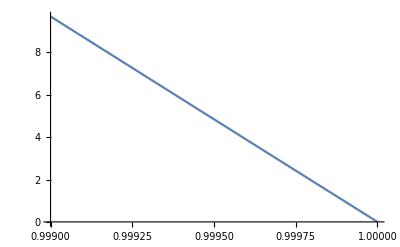

```mathematica
α=1/137;
ϵ=4;
s=1;
c=10^(-4);
V=.;
P[x_]:=(x-2)!!(-1)^((x-1)/2)/(2^((x-1)/2)*((x-1)/2)!);
V[z_]:=3/299.792458*(-1/2)^((z-1)/2)(2z+1)(z-2)!!/(2((z+1)/2)!);
F[n_,r_]:=(10^(-4)-c*r)/(c*r)^2*α*ϵ *Simplify[Sum[l^2*V[l]*P[l],{l,1,2*n+1}]-Sum[(2l)^2*V[2l]*P[2l],{l,1,n}]];
Plot[F[50,r],{r,0.999,1}]
```

```mathematica
n=.;
F[n_]:=Simplify[Sum[l^2*V[l]*P[l],{l,1,2*n+1}]-Sum[(2l)^2*V[2l]*P[2l],{l,1,n}]];
DiscretePlot[F[n],{n,0,5000}]
```

$Aborted

```mathematica
LegendreP[1711.,Cos[Pi/4]]
```

0.00877551

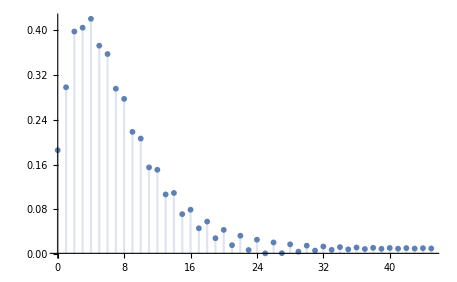

```mathematica
V=.;
α=1/137;
ϵ=4;
c=10^(-4);
V[z_]:=3/299.792458*(-1/2)^((z-1)/2)(2z+1)(z-2)!!/(2((z+1)/2)!);
G[l_,r_]:=-α*l*(c*r)^(l+1)*ϵ*(1-r^(-(2l+1)))/((ϵ-1)(l+1)+(l*ϵ+l+1)*r^(-(2l+1)))*V[l];
F[n_,x_]:=Simplify[Sum[c^(-(l+2))*(l+1)G[l,x],{l,1,2*n+1}]-Sum[c^(-(2l+2))*(2l+1)G[2l,x],{l,1,n}]];
DiscretePlot[Abs[F[n,0.9]],{n,0,45},PlotRange->All]
```

```mathematica
LegendreP[15.,Cos[Pi/4]]
```

0.0903925

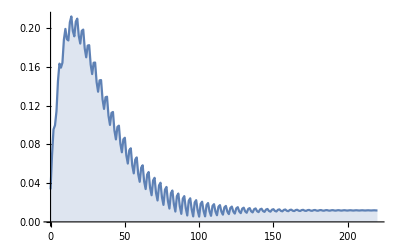

```mathematica
V=.;
α=1/137;
ϵ=4;
c=10^(4);
V[z_]:=3/299.792458*(-1/2)^((z-1)/2)(2z+1)(z-2)!!/(2((z+1)/2)!);
G[l_,r_]:=-α*l*r^(l+1)*ϵ*(1-r^(-(2l+1)))/((ϵ-1)(l+1)+(l*ϵ+l+1)*r^(-(2l+1)))*V[l];
Cr[m_,x_]:=-c^(1)*(m+1)*G[m,x]*LegendreP[m,Sqrt[1/2]];
Ct[m_,x_]:=-c^(1)*G[m,x]*m*(-LegendreP[m,Sqrt[1/2]]+Sqrt[2]*LegendreP[m-1,Sqrt[1/2]]);
Br[m_,y_]:=Simplify[Sum[Cr[l,y],{l,1,2*n+1}]-Sum[Cr[2*l,y],{l,1,n}]];
Bt[m_,y_]:=Simplify[Sum[Ct[l,y],{l,1,2*n+1}]-Sum[Ct[2*l,y],{l,1,n}]]

B[n_,y_]:=Sqrt[(Br[n,y])^2 +(Bt[n,y])^2];


DiscretePlot[Abs[B[n,0.98]],{n,0,220}]
```

```mathematica
Bt[0,0.98]
```

0.0826173+0. ⅈ

```mathematica
V=.;
α=1/137;
ϵ=4;
c=10^(-4);
a=.;
r=c;
R=10*c;
ζ=2*c;
θ=.;


V[z_]:=3/299.792458*(-1/2)^((z-1)/2)(2z+1)(z-2)!!/(2((z+1)/2)!);
G[l_,a_]:=-α*l*ϵ*(a^(2l+1)-r^(2l+1))*a^(l+1)*V[l]/(a^(2l+1)*(ϵ-1)(l+1)+(l*ϵ+l+1)*r^(2l+1));
F[n_,θ_]:=2*Pi*(Sum[G[l,a*c]/((ζ*Sec[θ])^l)((2*l+1)*LegendreP[l,Cos[θ]]*Sin[θ]-l*LegendreP[l-1,Cos[θ]]*Tan[θ]),{l,1,2*n+1}]-Sum[G[2*l,a*c]/((ζ*Sec[θ])^(2*l))((4*l+1)*LegendreP[2*l,Cos[θ]]*Sin[θ]-2*l*LegendreP[2*l-1,Cos[θ]]*Tan[θ]),{l,1,n}]);
(*Plot[FullSimplify[Integrate[F[10,θ],{θ,0,ArcTan[R/ζ]}]],{a,0,1}]
Integrate[F[10,θ],{θ,0,θ0}]*)
Table[Integrate[F[50,θ],{θ,0,ArcTan[R/ζ]}],
{a,{0.5,0.62}}]
```

{8.42086×10^-10+0. ⅈ,1.02465×10^-9+0. ⅈ}

```mathematica
α=1/137;
ϵ=4; (*permitividad relativa*)
c=10^(-4); (*factor para pasar de micras a cm 1micra=10^(-4)cm*)
r=c; (*este es r2, que es 1micra=10^(-4)cm*)
R=10*c; (*radio de la espira. se toman 10micras=10^(-3)cm*)
ζ=1.01*c; (*distancia vertical, debe ser mayor que r*)


V[z_]:=3/299.792458*(-1/2)^((z-1)/2)(2z+1)(z-2)!!/(2((z+1)/2)!);
(*esta es la función Vl*)
G[l_,a_]:=-α*l*ϵ*(a^(2l+1)-r^(2l+1))*a^(l+1)*V[l]/(a^(2l+1)*(ϵ-1)(l+1)+(l*ϵ+l+1)*r^(2l+1)); (*coeficiente Dl^3... mathematica no deja usar la letra D porque D es una función predefinidad del programa, pro eso la llamo G*)

F[n_,θ_]:=Sum[G[2*l+1,a]/((ζ*Sec[θ])^(2*l+1))((4*l+3)*LegendreP[2*l+1,Cos[θ]]*Sin[θ]-(2*l+1)*LegendreP[2*l,Cos[θ]]*Tan[θ]),{l,0,n}]
(*esta es la suma entre paréntesis de la expresión para el flujo magnético. Notese que como ya pase todo a cm, esta en statVcm=Gcm^2*)

(*Finalmente integro lo anterior desde 0 hasta arctan(R/ζ) y multiplico por 2pi como dice la expresión. esto finalmente da el flujo. yo había multiplicado la expresión por 10^(-4) porque pensé que estaba en statV*micra, pero no porque ya he pasado todo a cm*)
Table[2*Pi*Integrate[F[50,θ],{θ,0,ArcTan[R/ζ]}],
{a,{0.5*c,0.62*c}}]
```

{8.79769×10^-10,1.70145×10^-9}

C:\Users\DANIEL\Desktop\Discusión

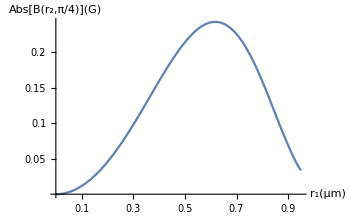

yesmaximize.png

```mathematica
SetDirectory[NotebookDirectory[]]
ticksv[min_,max_]:=Table[{i,Style[i,12],{.02,0},Directive[Black,Thick]},{i,0+0.05,max,0.05}]

ticksh[min_,max_]:=Table[{i,Style[i,12],{.02,0},Directive[Black,Thick]},{i,0+0.1,max,0.1}]

V=.;
α=1/137;
ϵ=4;
c=10^(4);
V[z_]:=3/299.792458*(-1/2)^((z-1)/2)(2z+1)(z-2)!!/(2((z+1)/2)!);
G[l_,r_]:=-α*l*r^(l+1)*ϵ*(1-r^(-(2l+1)))/((ϵ-1)(l+1)+(l*ϵ+l+1)*r^(-(2l+1)))*V[l];
Cr[m_,x_]:=-c^(1)*(m+1)*G[m,x]*LegendreP[m,Sqrt[1/2]];
Ct[m_,x_]:=-c^(1)*G[m,x]*m*(-LegendreP[m,Sqrt[1/2]]+Sqrt[2]*LegendreP[m-1,Sqrt[1/2]]);
Br[m_,y_]:=Simplify[Sum[Cr[l,y],{l,1,2*n+1}]-Sum[Cr[2*l,y],{l,1,n}]];
Bt[m_,y_]:=Simplify[Sum[Ct[l,y],{l,1,2*n+1}]-Sum[Ct[2*l,y],{l,1,n}]]

B[n_,y_]:=Sqrt[(Br[n,y])^2 +(Bt[n,y])^2];
yes=Plot[Abs[B[400,y]],{y,0,0.95},AxesLabel->{Style[Subscript[r,1][μm],12],Style[Abs["B" [ Subscript[r,2],"π/4"]][G],12]},AxesStyle->Black,Ticks->{ticksh,ticksv},ImageSize->350]
Export["yesmaximize.png",yes,ImageResolution->600]
```

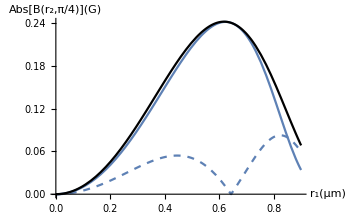

```mathematica
yes=Show[Plot[Abs[Br[40,y]],{y,0,0.9},AxesLabel->{Style[Subscript[r,1][μm],12],Style[Abs["B" [ Subscript[r,2],"π/4"]][G],12]},AxesStyle->Black,ImageSize->350],Plot[Abs[Bt[40,y]],{y,0,0.9},AxesLabel->{Style[Subscript[r,1][μm],12],Style[Abs["B" [ Subscript[r,2],"π/4"]][G],12]},PlotStyle->Dashed,AxesStyle->Black,ImageSize->350],
Plot[Abs[B[40,y]],{y,0,0.9},AxesLabel->{Style[Subscript[r,1][μm],12],Style[Abs["B" [ Subscript[r,2],"π/4"]][G],12]},PlotStyle->Black
,AxesStyle->Black,ImageSize->350]]
```